```mathematica
ComplexPlot[Fibonacci[n],{n,-100-100I,100+100I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[Fibonacci[n],{n,-10-10 I,10+10 I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics-

```mathematica
ComplexPlot[Sqrt[n] {Cos[2 Pi n GoldenRatio],Sin[2 Pi n GoldenRatio]},{n,-100,100},ColorFunction->"CyclicLogAbsArg"]
```

ComplexPlot::plld: Corners for n in {n,-100,100} must have distinct machine-precision real and imaginary parts.

ComplexPlot[√n {Cos[2 π n GoldenRatio],Sin[2 π n GoldenRatio]},{n,-100,100},ColorFunction→CyclicLogAbsArg]

```mathematica
SetAttributes[ConsList,HoldRest]
SetAttributes[ConsTree,HoldRest]

InfiniteSteps[head_,ID_,step_]:=ConsList[ID,InfiniteSteps[head,head@@{ID,step},step]]

InputSequence[func_,nSeq_,l_List]:=With[{mem=createMemory[l,Length[l]]},With[{refInd=createReferenceIndexes/@nSeq[Length[l]+1]},With[{lvar=func@@(mem⟦Sequence@@#1⟧&/@refInd)},ReplaceAll[mem,rep->ConsList[lvar,infiniteSequence[func,refInd,advanceMem[mem,lvar]]]]]]]

createReferenceIndexes[index_]:=Append[Take[ConsListRange[2,0],index-1],1]

createMemory[ID_List,n_]:=ConsList[First[ID],Evaluate[createMemory[Rest[ID],Length[Rest[ID]]]]]
createMemory[ID_List,1]:=ConsList[First[ID],rep]

infiniteSequence[func_,refInd_,mem_]:=With[{lvar=func@@(mem⟦Sequence@@#1⟧&/@refInd)},ConsList[lvar,infiniteSequence[func,refInd,advanceMem[mem,lvar]]]]

advanceMem[mem_,newID_]:=ReplaceAll[Level[mem,1][[2]],rep->ConsList[newID,rep]]

ConsList/:Take[ConsList[ID_,next_],n_]:=Prepend[Take[next,n-1],ID]/;n>1
ConsList/:Take[ConsList[ID_,next_],n_]:={ID}/;n==1
ConsList/:Take[ConsList[ID_,next_],n_]:={}/;n<=0

ConsList/:Take[ConsList[ID_,next_],{index_}]:=Take[next,{index-1}]
ConsList/:Take[ConsList[ID_,next_],{1}]:={ID}

ConsList/:Take[ConsList[ID_,next_],{start_,stop_,step_:1}]:=Take[next,{start-1,stop-1,step}]/;start>1&&start<=stop
ConsList/:Take[ConsList[ID_,next_],{start_,stop_,step_:1}]:=Prepend[Take[next,{step,stop-1,step}],ID]/;start==1&&start<stop
ConsList/:Take[ConsList[ID_,next_],{start_,stop_,step_:1}]:={ID}/;start==1&&stop==1
ConsList/:Take[ConsList[ID_,next_],{start_,stop_,step_:1}]:={}/;start>stop
ConsList/:Prepend[ConsList[ID_,next_],elem_]:=ConsList[elem,ConsList[ID,next]]
ConsList/:Select[ConsList[ID_,next_],condition_]:=If[condition[ID],ConsList[ID,Select[next,condition]],Select[next,condition]]
ConsList/:Map[f_,ConsList[ID_,next_]]:=ConsList[f[ID],Map[f,next]]

ConsList/:Map[f_,ConsList[ID_,next_],levelspec_]:=ConsList[Map[f,ID,{0,levelspec-1}],Map[f,next,levelspec]]
ConsList/:Map[f_,ConsList[ID_,next_],{levelspec_Integer?Positive}]:=ConsList[Map[f,ID,{levelspec-1}],Map[f,next,{levelspec}]]

ConsList/:Map[f_,ConsList[ID_,next_],{0}|{0,0}]:=f[ConsList[ID,next]]
ConsList/:Map[f_,ConsList[ID_,next_],0]:=ConsList[ID,next]
ConsList/:MapAt[f_,ConsList[ID_,next_],1]:=ConsList[f[ID],next]
ConsList/:MapAt[f_,ConsList[ID_,next_],n_Integer]:=ConsList[ID,MapAt[f,next,n-1]]/;n>1

ConsList/:MapAt[f_,ConsList[ID_,next_],i_List]:=If[MemberQ[i,{1}],ConsList[f[ID],MapAt[f,next,Delete[i,Position[i,{1}]]-1]],ConsList[ID,MapAt[f,next,i-1]]]
ConsList/:MapAt[f_,ConsList[ID_,next_],{{0}}]:=next
ConsList/:Part[ConsList[ID_,next_],i_]:=Part[next,i-1]
ConsList/:Part[ConsList[ID_,next_],1]:=ID

ConsList/:Part[ConsList[ID_,next_],m_;;n_;;s_:1]:=Part[next,m-1;;n-1;;s]/;m>1&&m<=n
ConsList/:Part[ConsList[ID_,next_],m_;;n_;;s_:1]:=Prepend[Part[next,s;;n-1;;s],ID]/;m==1&&m<n
ConsList/:Part[ConsList[ID_,next_],m_;;n_;;s_:1]:={ID}/;m==1&&n==1
(*ConsList/:Part[ConsList[ID_,next_],m_;;n_;;s_:1]:={}/;m>n*)
ConsList/:Part[ConsList[ID_,next_],m_;;n_;;s_:1]:={}
ConsListMapThread[f_,consList_List]:=ConsList[f@@(takeID/@consList),ConsListMapThread[f,takeNext/@consList]]
ConsList/:Partition[ConsList[ID_,next_],n_Integer,d_Integer]:=If[n!=d,With[{l=createPartition[ConsList[ID,next],n,d]},With[{clean=cleanForm[l,d]},ConsList[Take[clean,n],Partition[clean[[-1]],n,d]]]],Partition[ConsList[ID,next],n]]

ConsList/:Partition[ConsList[ID_,next_],n_Integer]:=With[{l=createPartition[ConsList[ID,next],n,n]},ConsList[Take[l,n],Partition[l[[-1]],n]]]
cleanForm[l_,d_]:=With[{parts=TakeDrop[l,{d}]},Append[Insert[parts[[2]],parts[[1]][[1]][[1]],d],parts[[1]][[1]][[2]]]]

createPartition[ConsList[ID_,next_],n_,d_]:=Prepend[createPartition[next,n-1,d-1],ID]/;n!=1&&d!=1
createPartition[ConsList[ID_,next_],n_,d_]:=Prepend[createPartition[next,n-1,d-1],{ID,next}]/;d==1&&n!=1
createPartition[ConsList[ID_,next_],n_,d_]:={ID,next}/;n==1&&d==1
createPartition[ConsList[ID_,next_],n_,d_]:={ID}/;n==1&&d!=1
ConsList/:Drop[ConsList[ID_,next_],n_Integer]:=Drop[next,n-1]
ConsList/:Drop[ConsList[ID_,next_],1]:=next

ConsList/:Drop[ConsList[ID_,next_],{n_Integer}]:=ConsList[ID,Drop[next,{n-1}]]
ConsList/:Drop[ConsList[ID_,next_],{1}]:=next

ConsList/:Drop[ConsList[ID_,next_],{m_,n_,s_:1}]:=ConsList[ID,Drop[next,{m-1,n-1,s}]]/;m>1&&m<=n

ConsList/:Drop[ConsList[ID_,next_],{m_,n_,s_:1}]:=Drop[next,{s,n-1,s}]/;m==1&&m<n

ConsList/:Drop[ConsList[ID_,next_],{m_,n_,s_:1}]:=next/;m==1&&n==1

ConsList/:Drop[ConsList[ID_,next_],{m_,n_,s_:1}]:=ConsList[ID,next]/;m>n
ConsList/:FoldList[f_,x_,ConsList[ID_,next_]]:=ConsList[x,FoldList[f,f@@{ID,x},next]]

ConsList/:FoldList[f_,ConsList[ID_,next_]]:=ConsList[ID,FoldList[f,replaceID[next,f@@{ID,takeID[next]}]]]
ConsList/:Riffle[ConsList[ID1_,next1_],ConsList[ID2_,next2_]]:=ConsList[ID1,ConsList[ID2,Riffle[next1,next2]]]

ConsList/:Riffle[ConsList[ID_,next_],x_,n_:2]:=ConsList[ID,extendRiffle[next,x,n-1,n]]

extendRiffle[ConsList[ID_,next_],x_,n_,max_]:=ConsList[ID,extendRiffle[next,x,n-1,max]]
extendRiffle[ConsList[ID_,next_],x_,1,max_]:=ConsList[x,extendRiffle[ConsList[ID,next],x,max,max]]
ConsList/:FirstPosition[ConsList[ID_,next_],searchID_]:=With[{index=1},If[searchID==ID,index,searchPosition[next,searchID,index+1]]]
searchPosition[ConsList[ID_,next_],searchID_,index_]:=If[searchID==ID,{index},searchPosition[next,searchID,index+1]]

Take[InputSequence[#1+#2&,{#-1,#-2}&,{1,1}],30]
fib=%[[30]]/%[[29]]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}

832040/514229

```mathematica
N[832040/514229]
```

1.61803

```mathematica
GoldenRatio
```

GoldenRatio

```mathematica
N[GoldenRatio]
```

1.61803

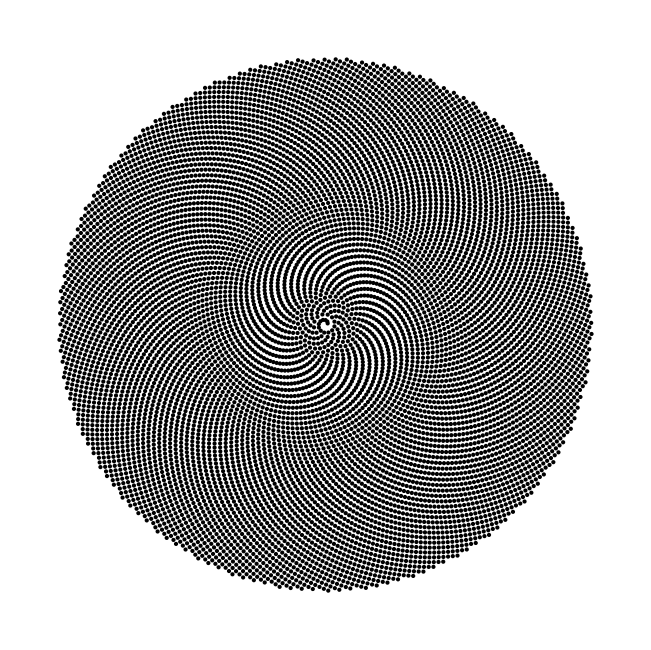

```mathematica
Graphics[Point[Table[Sqrt[n] {Cos[0.1Pi n fib],Sin[0.1Pi n fib]},{n,10000}]]]
```

```mathematica
Graphics[Point[Table[Sqrt[n] {Cos[20 Pi n GoldenRatio],Sin[20 Pi n GoldenRatio]},{n,50000}]]]
```

-Graphics-

```mathematica
Graphics[Point[Table[Sqrt[n] {Cos[Pi n GoldenRatio],Sin[Pi n GoldenRatio]},{n,50000}]]]
```

-Graphics-